Initial Graph:

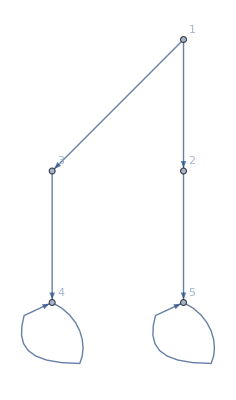

Frequency Vector: {{{1,γ,0,0,γ^2/(1-γ)},{1,0,γ,γ^2/(1-γ),0}},{{0,1,0,0,γ/(1-γ)}},{{0,0,1,γ/(1-γ),0}},{{0,0,0,1/(1-γ),0}},{{0,0,0,0,1/(1-γ)}}}

#############################################################################################

Equation List: {r[1]+γ r[2]+(γ^2 r[5])/(1-γ),r[1]+γ r[3]+(γ^2 r[4])/(1-γ)}

+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++

Current Frequency Index: 1

Inequalities used: r[2]+γ (r[3]+r[5])>r[3]+γ (r[2]+r[4])

Integration: Piecewise[{{-(-1+8 γ+17 γ^2+16 γ^3)/(120 (-1+γ) γ), 2 γ≥1}, {(γ (-40+90 γ-65 γ^2+16 γ^3))/(120 (-1+γ)^3), True}}]

Measure: 1/2

+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++

Current Frequency Index: 2

Inequalities used: r[2]+γ (r[3]+r[5])<r[3]+γ (r[2]+r[4])

Integration: Piecewise[{{-(-1+8 γ+17 γ^2+16 γ^3)/(120 (-1+γ) γ), 2 γ≥1}, {(γ (-40+90 γ-65 γ^2+16 γ^3))/(120 (-1+γ)^3), True}}]

Measure: 1/2

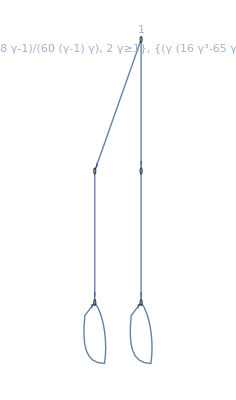

```mathematica
(*1*)

maxK = 4;
(*
For[k = 2, k≤  maxK, k++,
vertexAndNodes1 = {1->2 ,2->2,1->3};
If[k ==2,
vertexAndNodes1 = {1->2 ,2->2,1->3, 3->3};
, (*Else, k>2*)
For[i = 3, i<=k, i++,
AppendTo[vertexAndNodes1, i->i+1];
If[i ==k,
AppendTo[vertexAndNodes1, i+1->3];
,
];
];
];
fin = powerOfGraph[vertexAndNodes1, "First", "Measure"];
Print[fin];
];
*)

maxK = 4;
(*
For[k = 2, k≤  maxK, k++,
(*2*)

vertexAndNodes2 = {}; 
For[i = 1, i<=k, i++,
AppendTo[vertexAndNodes2, i->i+1];
If[i ==k,
AppendTo[vertexAndNodes2, 1->i+1];
AppendTo[vertexAndNodes2, i+1->i+1];
,
];
];
(*
powerOfGraph[vertexAndNodes2, "First", "Basic"]
*)
fin = powerOfGraph[vertexAndNodes2, "First", "Measure"];
Print[fin];
];
*)
(*3*)
vertexAndNodes3 = {1->2, 2->3, 1->3, 3->4, 4->4, 2->5, 5->5};
vertexAndNodes3 = {1->2,  1->3, 3->4, 4->4, 2->5, 5->5};
powerOfGraph[vertexAndNodes3, "First", "Basic"]
vertexAndNodes3 = {1->2,2->1, 2->2, 1->3, 3->4, 4->4};
vertexAndNodes3 = {1->1, 1->2, 2->3, 3->2, 1->3};


(*4*)
vertexAndNodes4 = {1->2, 2->2, 1->3, 3->4, 4->4, 3->5, 5->5};
(*
powerOfGraph[vertexAndNodes4, "First", "Measure"]
*)
(*5*)
vertexAndNodes5 = {1->2, 1->3, 1->4, 2->1, 2->3, 2->4, 3->1, 3->2, 3->4, 4->1, 4->2, 4->3};
vertexAndNodes5 = {1->2, 1->3, 2->1, 2->3,3->1, 3->2};
```